# Function:

```mathematica
f[x_] := (2x + 3)/(3x - 1)
```

```mathematica
f[2]
```

7/5

```mathematica
N[%]
```

1.4

```mathematica
f'[x]
```

-(3 (3+2 x))/(-1+3 x)^2+2/(-1+3 x)

```mathematica
D[x^2,x]
```

```mathematica
2 x
```

```mathematica
f''[x]
```

(18 (3+2 x))/(-1+3 x)^3-12/(-1+3 x)^2

```mathematica
D[x^2,{x, 2}]
```

2

```mathematica
D[Cos[x]+x, {x, 2}]
```

-Cos[x]

```mathematica
Integrate[√x,x]
```

(2 x^(3/2))/3

```mathematica
Integrate[√x,{x,0,2}]
```

(4 √2)/3

```mathematica
N[Integrate[√x,{x,0,2}]]
```

1.88562

```mathematica
D[x^(x^x),x]
```

x^(x^x) (x^(-1+x)+x^x Log[x] (1+Log[x]))

```mathematica
Clear[a]
```

```mathematica
D[a^(a^x),x]
```

a^(a^x+x) Log[a]^2

```mathematica
D[x^(1/x),x]
```

x^(1/x) (1/x^2-Log[x]/x^2)

D[Sin[x^2],x]  Chain Rule

2 x Cos[x^2]

D[x*Sin[x], x]      Product Rule

x Cos[x]+Sin[x]

## Simplifying Algebraic Expressions:

```mathematica
Simplify[x^2 + 2x + 1]
```

(1+x)^2

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
Simplify[Integrate[1/(x^4-1),x]]
```

1/4 (-2 ArcTan[x]+Log[1-x]-Log[1+x])

```mathematica
FullSimplify[Integrate[1/(x^4-1),x]]
```

1/2 (-ArcTan[x]-ArcTanh[x])

```mathematica
FullSimplify[Integrate[1/(x^4-1),{x,-Pi/4,Pi/4}]]
```

```mathematica
-ArcTan[π/4]-ArcTanh[π/4]
```

```mathematica
Solve[x^5-4x+5==0,x]
```

{{x→Root-1.63Root[5-4 #1+#1^5&,1]-1.6304355271660866},{x→Root-0.237-1.52 ⅈRoot[5-4 #1+#1^5&,2]-0.23709440664517753},{x→Root-0.237+1.52 ⅈRoot[5-4 #1+#1^5&,3]-0.23709440664517753},{x→Root1.05-0.443 ⅈRoot[5-4 #1+#1^5&,4]1.052312170228221},{x→Root1.05+0.443 ⅈRoot[5-4 #1+#1^5&,5]1.052312170228221}}

```mathematica
NSolve[x^5-4x+5==0,x]
```

{{x→-1.63044},{x→-0.237094-1.51552 ⅈ},{x→-0.237094+1.51552 ⅈ},{x→1.05231-0.442637 ⅈ},{x→1.05231+0.442637 ⅈ}}

```mathematica
NSolve[x^5-4x+5==0,x, Reals]
```

{{x→-1.63044}}

```mathematica
Solve[{x^2+y^3==1, 2x+3y==6},{x,y}]
```

{{x→3/2 (2-Root-4.59Root[32-36 #1+9 #1^2+4 #1^3&,1]-4.590317289487992),y→Root-4.59Root[32-36 #1+9 #1^2+4 #1^3&,1]-4.590317289487992},{x→3/2 (2-Root1.17-0.611 ⅈRoot[32-36 #1+9 #1^2+4 #1^3&,2]1.170158644743996),y→Root1.17-0.611 ⅈRoot[32-36 #1+9 #1^2+4 #1^3&,2]1.170158644743996},{x→3/2 (2-Root1.17+0.611 ⅈRoot[32-36 #1+9 #1^2+4 #1^3&,3]1.170158644743996),y→Root1.17+0.611 ⅈRoot[32-36 #1+9 #1^2+4 #1^3&,3]1.170158644743996}}

```mathematica
NSolve[{x^2+y^3==1, 2x+3y==6},{x,y}]
```

{{x→9.88548,y→-4.59032},{x→1.24476-0.916754 ⅈ,y→1.17016+0.611169 ⅈ},{x→1.24476+0.916754 ⅈ,y→1.17016-0.611169 ⅈ}}

```mathematica
(*Integrate:√(1-Sin[2x]), (1-Cos[2x])/(1+Cos[2x]),(x^3+1)/(x+1),Sin[x]/(3+4*Cos[x]),1/(x(1+Log[x]))*)
```

```mathematica
Integrate[√(1-Sin[2x]),x]
```

((Cos[x]+Sin[x]) √(1-Sin[2 x]))/(Cos[x]-Sin[x])

```mathematica
Integrate[(1-Cos[2x])/(1+Cos[2x]),x]
```

-x+Tan[x]

```mathematica
Integrate[(x^3+1)/(x+1),x]
```

x-x^2/2+x^3/3

```mathematica
Integrate[Sin[x]/(3+4*Cos[x]),x]
```

-1/4 Log[3+4 Cos[x]]

```mathematica
Integrate[1/(x(1+Log[x])),x]
```

Log[1+Log[x]]

```mathematica
FullSimplify[Integrate[√(1-Sin[2x]),{x,0,Pi}]]
```

2 √2

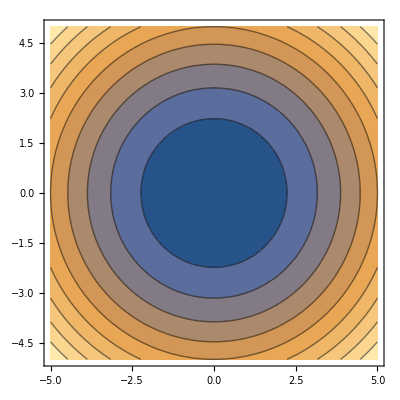

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5}]
```

```mathematica
Plot3D[x^2+y^2,{x,-5,5},{y,-5,5}]
```

-Graphics3D-